```mathematica
Gilpin =NDSolve[{x'[t]==x[t]-0.001 x[t]^2-0.001 x[t] y[t]-0.01 x[t] z[t],y'[t]==y[t]-0.0015 x[t] y[t]-0.001 y[t]^2-0.001 y[t] z[t],z'[t]==-z[t]+0.005 x[t] z[t]+0.0005 y[t] z[t],x[0]==y[0]==z[0]==10},{x[t],y[t],z[t]},{t,0,300},MaxSteps->3000]
```

{{x[t]→InterpolatingFunction[{{0., 300.}}, <>][t],y[t]→InterpolatingFunction[{{0., 300.}}, <>][t],z[t]→InterpolatingFunction[{{0., 300.}}, <>][t]}}

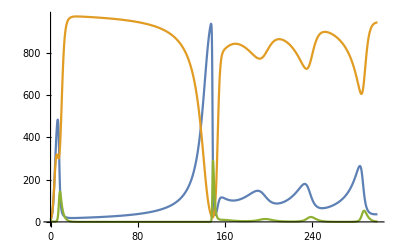

```mathematica
Plot[Evaluate[{x[t],y[t],z[t]} /. Gilpin], {t,0,300}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]} /. Gilpin], {t,0,300}, PlotRange -> All, PlotPoints-> 3000]
```

-Graphics3D-

```mathematica
http://artemis.wszib.edu.pl/~sloot/3_6.html
```